```mathematica
通电螺线管的磁场分布
```

```mathematica
毕-奥公式里的叉乘运算
```

```mathematica
P1={R Cos[2π t],R Sin[2 π t],k t};
P={x,y,z};r12=P-P1;
dl1=D[P1,t];
cro=dl1×r12//FullSimplify
Clear[P,P1,r12,dl1,cro]
```

{(y(x) (R sin(2 π t) (1/(((1.-1. x)^2+(y(x))^2)^(3/2))-1./(((y(x))^2+(1. x+1.)^2)^(3/2)))+R t cos(2 π t) (6.28319/(((y(x))^2+(1. x+1.)^2)^(3/2))-6.28319/(((1.-1. x)^2+(y(x))^2)^(3/2)))+y (1/(((y(x))^2+(1. x+1.)^2)^(3/2))-1./(((1.-1. x)^2+(y(x))^2)^(3/2)))))/((x-1.)/(((y(x))^2+(x-1.)^2)^(3/2))-(x+1.)/(((y(x))^2+(x+1.)^2)^(3/2)))+2 π R z cos(2 π t),(y(x) (R t sin(2 π t) (6.28319/(((y(x))^2+(1. x+1.)^2)^(3/2))-6.28319/(((1.-1. x)^2+(y(x))^2)^(3/2)))+R cos(2 π t) (1/(((y(x))^2+(1. x+1.)^2)^(3/2))-1./(((1.-1. x)^2+(y(x))^2)^(3/2)))+x (1/(((1.-1. x)^2+(y(x))^2)^(3/2))-1./(((y(x))^2+(1. x+1.)^2)^(3/2)))))/((x-1.)/(((y(x))^2+(x-1.)^2)^(3/2))-(x+1.)/(((y(x))^2+(x+1.)^2)^(3/2)))+2 π R z sin(2 π t),2 π R (R-x cos(2 π t)-y sin(2 π t))}

```mathematica
距离公式化简
```

```mathematica
P1={R Cos[2π t],R Sin[2 π t],k t};
P={x,y,z};
r12=P-P1;
Expand[r12.r12]//FullSimplify
Clear[P,P1,r12]
```

(t^2 (y(x))^2 (-2./(((y(x))^2+(1. x+1.)^2)^(3/2) ((1.-1. x)^2+(y(x))^2)^(3/2))+1/(((y(x))^2+(x-1.)^2)^3)+1/(((y(x))^2+(x+1.)^2)^3)))/(((x-1.)/(((y(x))^2+(x-1.)^2)^(3/2))-(x+1.)/(((y(x))^2+(x+1.)^2)^(3/2)))^2)+(2 t z y(x) (1/(((y(x))^2+(1. x+1.)^2)^(3/2))-1./(((1.-1. x)^2+(y(x))^2)^(3/2))))/((x-1.)/(((y(x))^2+(x-1.)^2)^(3/2))-(x+1.)/(((y(x))^2+(x+1.)^2)^(3/2)))+R^2-2 R x cos(2 π t)-2 R y sin(2 π t)+x^2+y^2+z^2

```mathematica
三个方向磁场描绘
```

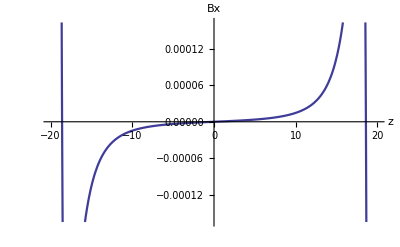

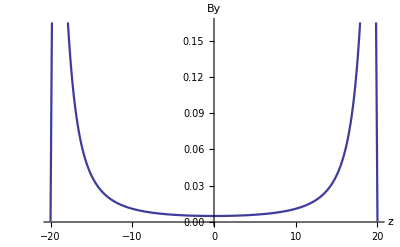

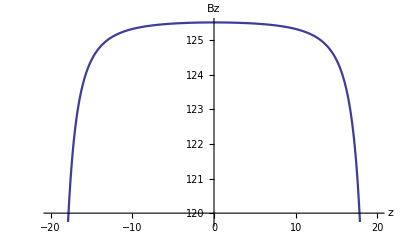

```mathematica
R=1;k=0.1;m=200;
Bx[x_,y_,z_]:=
NIntegrate[
(-k y+2 π R (-k t+z) Cos[2 π t]+k R Sin[2 π t])/
(R^2+x^2+y^2+(-k t+z)^2-
2 R (x Cos[2 π t]+y Sin[2 π t]))^(3/2),{t,-m,m},
MaxRecursion->20];
By[x_,y_,z_]:=
NIntegrate[
(k x-k R Cos[2 π t]+2 π R (-k t+z) Sin[2 π t])/
(R^2+x^2+y^2+(-k t+z)^2-
2 R (x Cos[2 π t]+y Sin[2 π t]))^(3/2),{t,-m,m},
MaxRecursion->20];
Bz[x_,y_,z_]:=
NIntegrate[(2 π R (R-x Cos[2 π t]-y Sin[2 π t]))/
(R^2+x^2+y^2+(-k t+z)^2-
2 R (x Cos[2 π t]+y Sin[2 π t]))^(3/2),{t,-m,m},
MaxRecursion->20];
(*...............................*)
Plot[Bx[0,0,z],{z,-m k,m k},AxesLabel->{"z","Bx"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[By[0,0,z],{z,-m k,m k},AxesLabel->{"z","By"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Plot[Bz[0,0,z],{z,-m k,m k},AxesLabel->{"z","Bz"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[R,k,Bx,By,Bz,m]
```

```mathematica
线圈轴线上三个磁场分量
```

{2012,2,9,20,34,19.7558593}

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.17181×10^-7 and 1.57491×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.33227×10^-15 and 1.57037×10^-13 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.17181×10^-7 and 1.56433×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

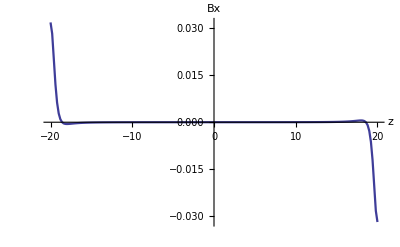

e:/data/pBx.dat

{2012,2,9,20,35,24.9638671}

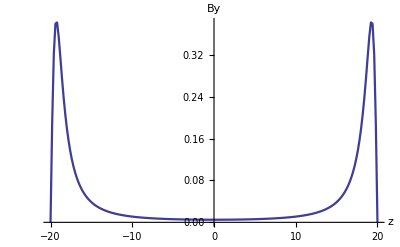

e:/data/pBy.dat

{2012,2,9,20,35,56.2109375}

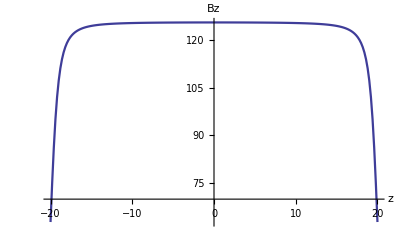

e:/data/pBz.dat

{2012,2,9,20,35,57.4941406}

```mathematica
R=1;k=0.1;m=200;
Bx[z_]:=
NIntegrate[
(2 π R (-k t+z) Cos[2 π t]+k R Sin[2 π t])/
(R^2+(-k t+z)^2)^(3/2),{t,-m,m},
MaxRecursion->20];
By[z_]:=
NIntegrate[
(-k R Cos[2 π t]+2 π R (-k t+z) Sin[2 π t])/
(R^2+(-k t+z)^2)^(3/2),{t,-m,m},
MaxRecursion->20];
Bz[z_]:=
NIntegrate[2 π R^2/
(R^2+(-k t+z)^2)^(3/2),{t,-m,m},
MaxRecursion->20];
n=200;δz=2m k/n;
pz=Table[z,{z,-m k,m k,δz}];
Date[]
pBx=Table[{z,Bx[z]},{z,pz}];
ListLinePlot[pBx,PlotRange->All,
AxesLabel->{"z","Bx"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Export["e:/data/pBx.dat",pBx]
Date[]
pBy=Table[{z,By[z]},{z,pz}];
ListLinePlot[pBy,PlotRange->All,
AxesLabel->{"z","By"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Export["e:/data/pBy.dat",pBy]
Date[]
pBz=Table[{z,Bz[z]},{z,pz}];
ListLinePlot[pBz,PlotRange->All,
AxesLabel->{"z","Bz"},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Export["e:/data/pBz.dat",pBz]
Date[]
Clear[R,k,Bx,By,Bz,m,n,pz,pBx,pBy,pBz]
```